```mathematica
(* Parametros *)
dt = 0.005;
ℏ = 1;
m = 1.9;
V0 = 0.21;
dx = 0.1;
xmin = -102.4;
xmax = 102.4;
Nn  = (xmax-xmin)/dx; (* Tamaño de los arrays *)

(* Array de espacios *)
xarray = Table[ i,{i,-1/2 Nn dx, 1/2 Nn dx, dx}];
dk = (2 π)/(Nn dx);
k0 = -1/2 Nn dk;
karray = Table[ k0 + i,{i,0, Nn dk, dk}];

(* Potencial *)
L = ℏ/(√(2 m));
ac = 3 L;
V[x_, a_, V0_] := (2V0/3) (UnitStep[x+2a] - UnitStep[x+a]) +(V0/2) (UnitStep[x+a] - UnitStep[x]) + V0 (UnitStep[x] - UnitStep[x-a]) +(V0/2) (UnitStep[x-a] - UnitStep[x - 2a])+(V0/8) (UnitStep[x-2a] - UnitStep[x-4a]);
varray =V[xarray, ac, V0];
zeroindex = 45;
Do[varray[[i]] = 10^20,{i,1,zeroindex }]
Do[varray[[i]] = 10^20,{i,Length[varray]-zeroindex ,Length[varray]}]

(* Array de funciones de onda *)
x0c = -60 L;
p0c = √(2 m  (0.2));
dp2 = p0c^2/80;
d = ℏ/(√(2 dp2));
k0c = p0c/ℏ; 

ψ0x[x_,a_,x0_, k0_] := 1/(√(a √π))ⅇ^(-1/2((x-x0)/a)^2+ⅈ x k0);
ψ0xarray = ψ0x[xarray, d, x0c, k0c];

(* Para graficar *)
scalegauss = 1/(√(d √π));
scalev0 = V0;
scale =0;
If[scalegauss > scalev0, scale = scalegauss, scale = scalev0];

(* Funciones *)
CF[ψxarray_]:= Module[{ψtmp},
ψtmp =ψxarray; 
Do[ψtmp[[i]] = 0.0,{i,1,zeroindex}];
Do[ψtmp[[i]] = 0.0,{i,Length[ψtmp]-zeroindex ,Length[ψtmp]}];
Return[ψtmp];
];
Discretize[ψxarray_] := ψxarray dx/(√(2 π))ⅇ^(-ⅈ k0 xarray);
Undiscretize[ψxarray_] := ψxarray (√(2 π))/dx ⅇ^(ⅈ k0 xarray);

Stepψx [ψxarray_, dt_] := ψxarray ⅇ^(-ⅈ/2 varray/ℏ dt);
Stepψk [ψkarray_, dt_] := ψkarray ⅇ^(-ⅈ/2(ℏ karray^2)/m dt);
Stepψ[ψxarray_] := Module[{ψmx,ψmk},
ψmx = CF[ψxarray];
ψmx = Stepψx[ψmx, dt];
ψmk = Fourier[ψmx];
ψmk = Stepψk[ψmk,dt];
ψmx = InverseFourier[ψmk];
ψmx = Stepψx[ψmx, dt];
Return[ψmx];
]
StepψForList[ψxarray_] := Module[{ψmx,ψmk},
ψmx = CF[ψxarray];
ψmx = Stepψx[Discretize[ψmx], dt];
ψmk = Fourier[ψmx];
ψmk = Stepψk[ψmk,dt];
ψmx = InverseFourier[ψmk];
ψmx = Stepψx[ψmx, dt];
Return[Undiscretize[ψmx]];
]
Evolve[ψxarray_, iter_]:= Module[{},
Print["t = " <> ToString[iter*dt]];
Return[Undiscretize[Nest[Stepψ,Discretize[ψxarray],iter]]];
]
EvolveList[ψxarray_, iter_]:= Module[{},
Print["t_max = " <> ToString[iter*dt]];
Return[NestList[StepψForList,ψxarray,iter]];
]
```

t = 20.

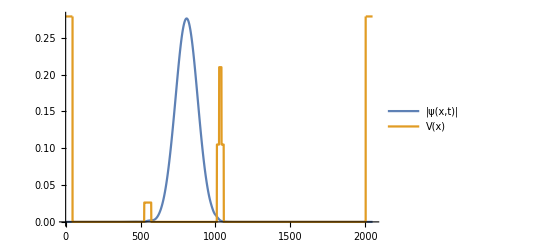

```mathematica
ListLinePlot[{Abs[Evolve[ψ0xarray,2000]],varray}, PlotRange->scale, PlotLegends->{"|ψ(x,t)|", "V(x)"}]
```

```mathematica
alist = Abs[EvolveList[ψ0xarray,40000]];
anim = Animate[ListLinePlot[{alist[[n]],varray}, PlotRange->scale, PlotLegends->{"|ψ(x,t)|", "V(x)"}],{n,1,Length[alist],1},AnimationRunning->False]
```

t_max = 200.

```mathematica
Export["anim.avi",anim]
```

anim.avi